```mathematica
SetDirectory["C:\\Users\\nemes\\OneDrive\\Documents\\Academics\\UChicago\\Research\\ACA-MTD"];
```

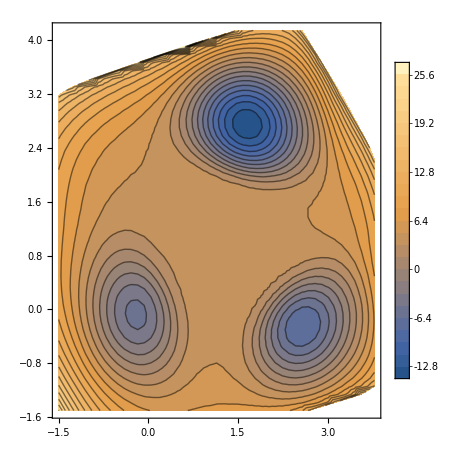

-Graphics3D-

```mathematica
domain={{-1.5,4},{-1.5,4.5}};
nbins=50;
data=ArrayReshape[ToExpression[StringSplit[ReadList["gaussian_50_7.out",String],{" ","[","]"}][[53]]],{nbins-1,nbins-1}];
ListContourPlot[Flatten[Table[
{(i-1)(domain[[1,2]]-domain[[1,1]])/nbins+domain[[1,1]],(j-1)(domain[[2,2]]-domain[[2,1]])/nbins+domain[[2,1]],data[[i,j]]},
{i,nbins-1},{j,nbins-1}
],1],PlotRange->All,Contours->25,PlotLegends->Automatic,AspectRatio->(4.1+1.5)/(3.4+1.5)]
ListPlot3D[Flatten[Table[
{(i-1)(domain[[1,2]]-domain[[1,1]])/nbins+domain[[1,1]],(j-1)(domain[[2,2]]-domain[[2,1]])/nbins+domain[[2,1]],data[[i,j]]},
{i,nbins-1},{j,nbins-1}
],1],PlotRange->All,ImageSize->Large]
```

```mathematica
cmapdensity=Blend[{RGBColor[{255,247,243}/255],RGBColor[{145,0,63}/255]},Tanh[0.5#]]&;
```

```mathematica
{xi,xf,dx}={0.8119808494874291,2.5321276069578134,0.006745673558707389};
{yi,yf,dy}={2.1733229207094564,3.4985603526920244,0.005197009537186541};
dens=ToExpression[StringSplit[StringReplace[ReadList["kde.out",String],{"e+":>"*^","e-":>"*^-"}]]];
fes=-Log[dens];
ListContourPlot[Flatten[Table[{xi+i dx,yi+j dy,dens[[i,j]]},{i,256},{j,256}],1],
ColorFunction->cmapdensity,ColorFunctionScaling->False,PlotRange->All,Contours->10,AspectRatio->(3.5-2.2)/(2.5-0.8)]
```

-Graphics-

```mathematica
ListContourPlot[Flatten[Table[{xi+i dx,yi+j dy,fes[[i,j]]},{i,256},{j,256}],1],PlotLegends->Automatic,Contours->{25,15,5,3,2,0.25},AspectRatio->(3.5-2.2)/(2.5-0.8)]
```

-Graphics-

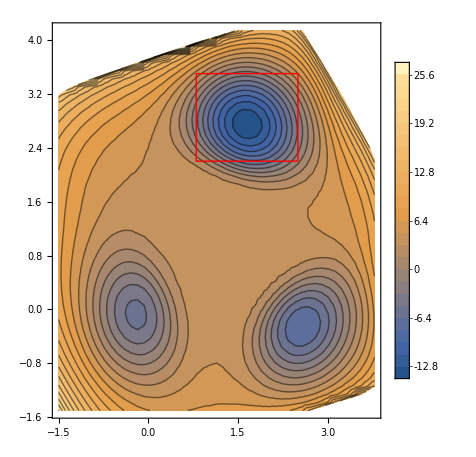

```mathematica
Show[
ListContourPlot[Flatten[Table[
{(i-1)(domain[[1,2]]-domain[[1,1]])/nbins+domain[[1,1]],(j-1)(domain[[2,2]]-domain[[2,1]])/nbins+domain[[2,1]],data[[i,j]]},
{i,nbins-1},{j,nbins-1}
],1],PlotRange->All,Contours->25,PlotLegends->Automatic,AspectRatio->(4.1+1.5)/(3.4+1.5)],
Graphics[{Red,Line[{{0.8,2.2},{2.5,2.2},{2.5,3.5},{0.8,3.5},{0.8,2.2}}]}]
]
```

```mathematica
{xi,xf,dx}={0.8119808494874291,2.5321276069578134,0.006745673558707389};
{yi,yf,dy}={2.1733229207094564,3.4985603526920244,0.005197009537186541};
dens=ToExpression[StringSplit[StringReplace[ReadList["res1.out",String],{"e+":>"*^","e-":>"*^-"}]]];
ListContourPlot[Flatten[Table[{xi+i dx,yi+j dy,dens[[i,j]]},{i,256},{j,256}],1],
ColorFunction->cmapdensity,ColorFunctionScaling->False,PlotRange->All,Contours->7,AspectRatio->(3.5-2.2)/(2.5-0.8)]
```

-Graphics-

```mathematica
{xi,xf,dx}={0.8119808494874291,2.5321276069578134,0.006745673558707389};
{yi,yf,dy}={2.1733229207094564,3.4985603526920244,0.005197009537186541};
dens=ToExpression[StringSplit[StringReplace[ReadList["res2.out",String],{"e+":>"*^","e-":>"*^-"}]]];
ListContourPlot[Flatten[Table[{xi+i dx,yi+j dy,dens[[i,j]]},{i,256},{j,256}],1],
ColorFunction->cmapdensity,ColorFunctionScaling->False,PlotRange->All,Contours->6,AspectRatio->(3.5-2.2)/(2.5-0.8)]
```

-Graphics-

```mathematica
{xi,xf,dx}={0.8119808494874291,2.5321276069578134,0.006745673558707389};
{yi,yf,dy}={2.1733229207094564,3.4985603526920244,0.005197009537186541};
dens=ToExpression[StringSplit[StringReplace[ReadList["res3.out",String],{"e+":>"*^","e-":>"*^-"}]]];
ListContourPlot[Flatten[Table[{xi+i dx,yi+j dy,dens[[i,j]]},{i,256},{j,256}],1],
ColorFunction->cmapdensity,ColorFunctionScaling->False,PlotRange->All,Contours->5,AspectRatio->(3.5-2.2)/(2.5-0.8)]
```

-Graphics-

```mathematica
{xi,xf,dx}={0.8119808494874291,2.5321276069578134,0.006745673558707389};
{yi,yf,dy}={2.1733229207094564,3.4985603526920244,0.005197009537186541};
dens=ToExpression[StringSplit[StringReplace[ReadList["res4.out",String],{"e+":>"*^","e-":>"*^-"}]]];
ListContourPlot[Flatten[Table[{xi+i dx,yi+j dy,dens[[i,j]]},{i,256},{j,256}],1],
ColorFunction->cmapdensity,ColorFunctionScaling->False,PlotRange->All,Contours->4,AspectRatio->(3.5-2.2)/(2.5-0.8)]
```

-Graphics-

```mathematica
{xi,xf,dx}={0.8119808494874291,2.5321276069578134,0.006745673558707389};
{yi,yf,dy}={2.1733229207094564,3.4985603526920244,0.005197009537186541};
dens=ToExpression[StringSplit[StringReplace[ReadList["res5.out",String],{"e+":>"*^","e-":>"*^-"}]]];
ListContourPlot[Flatten[Table[{xi+i dx,yi+j dy,dens[[i,j]]},{i,256},{j,256}],1],
ColorFunction->cmapdensity,ColorFunctionScaling->False,PlotRange->All,Contours->3,AspectRatio->(3.5-2.2)/(2.5-0.8)]
```

-Graphics-